```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
new=Association[Import["Trajectory1PAT1R.h5","Rules"]];
orig=Association[Import["Trajectory1PAT1R_orig.h5","Rules"]];
```

```mathematica
yGrid=new["Data"]["/Flux/Energy/0PA/Grid"];
ℱℋy=new["Data"]["/Flux/Energy/0PA/Horizon"];
ℱℐy=new["Data"]["/Flux/Energy/0PA/Infinity"];
```

```mathematica
pGrid=orig["Data"]["/Flux/Energy/0PA/Grid"];
ℱℋp=orig["Data"]["/Flux/Energy/0PA/Horizon"];
ℱℐp=orig["Data"]["/Flux/Energy/0PA/Infinity"];
```

```mathematica
ℱℐyS=Interpolation[Transpose[{yGrid,ℱℐy}],Method->"Spline"];
```

```mathematica
ℱℐySdownsampled=Interpolation[Downsample[Transpose[{yGrid,ℱℐy}],{2,1}],Method->"Spline"];
```

```mathematica
ℱℐy12=Interpolation[Transpose[{yGrid,ℱℐy}],InterpolationOrder->12];
```

```mathematica
ℱℐy4=Interpolation[Transpose[{yGrid,ℱℐy}],InterpolationOrder->4];
```

```mathematica
ℱℐpS=Interpolation[Transpose[{pGrid,ℱℐp}],Method->"Spline"];
```

```mathematica
ℱℐpSdownsampled=Interpolation[Downsample[Transpose[{pGrid,ℱℐp}],{2,1}],Method->"Spline"];
```

```mathematica
ℱℐp8=Interpolation[Transpose[{pGrid,ℱℐp}],InterpolationOrder->8];
```

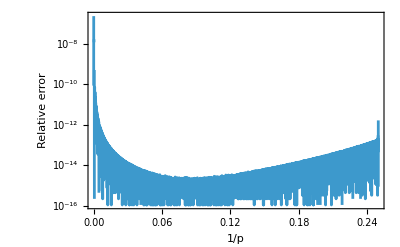

```mathematica
LogPlot[Abs[1-ℱℐyS[y]/ℱℐy12[y]],{y,0,1/4},PlotRange->All,PlotTheme->"Detailed",PlotLegends->None,FrameLabel->{"1/p","Relative error"}]
```

```mathematica
Rasterize@GraphicsRow[{LogPlot[{Abs[1-ℱℐySdownsampled[y]/ℱℐy12[y]],Abs[1-ℱℐyS[y]/ℱℐy12[y]],Abs[1-ℱℐy4[y]/ℱℐy12[y]]},{y,0,1/100},PlotRange->All],LogPlot[{Abs[1-ℱℐySdownsampled[y]/ℱℐy12[y]],Abs[1-ℱℐyS[y]/ℱℐy12[y]],Abs[1-ℱℐy4[y]/ℱℐy12[y]]},{y,0,1/4},PlotRange->All],LogPlot[{Abs[1-ℱℐySdownsampled[y]/ℱℐy12[y]],Abs[1-ℱℐyS[y]/ℱℐy12[y]],Abs[1-ℱℐy4[y]/ℱℐy12[y]]},{y,99/400,1/4},PlotRange->All]},ImageSize->1200]
```

-Graphics-

```mathematica
Rasterize@LogPlot[{Abs[1-ℱℐySdownsampled[y]/ℱℐy12[y]],Abs[1-ℱℐyS[y]/ℱℐy12[y]],Abs[1-ℱℐpS[1/y]/(32/5 y^5 ℱℐy12[y])]},{y,1/30,1/6},PlotRange->All]
```

-Graphics-